```mathematica
<<"C:\\Users\\王鑫\\Desktop\\maxwell_dis_par_100_win100_and_400_win70.mx"
```

=== [1/3] 正在智能检索内核已导入的数据... ===

当前内存检测状态:

- 存在 eigenVals: False

- 存在 lapMat: False

- 存在 universe: True

[接管成功] 发现 universe，正在重构无向图并提取矩阵...

[矩阵构建完成] 正在提取最后 500 个物理特征值...

Eigenvalues::maxit2: 警告：Arnoldi 算法已经达到最大迭代次数 1000，而没有收敛到指定的容差，但是已经返回了当前最佳计算值. 您可以利用 Method -> {Arnoldi, opts} 使用方法选项来增加基本向量的大小、最大迭代次数、降低容差，或者将估计值作为平移使用，以上方法任选其一都可能有帮助.

[就绪] 成功清洗并挂载了 499 个非零物理特征值。

=== [2/3] 启动解析热核尺度扫描 (纯英文变量，杜绝乱码) ===

正在执行对数空间尺度漫游...

=== [3/3] 连续谱维度相变图纸 ===

▶ 紫外普朗克极限 D_UV ≈ 0.

▶ 红外经典统高原 D_IR ≈ 2.369

▶ 维度流动净跨度 δD  ≈ 2.369

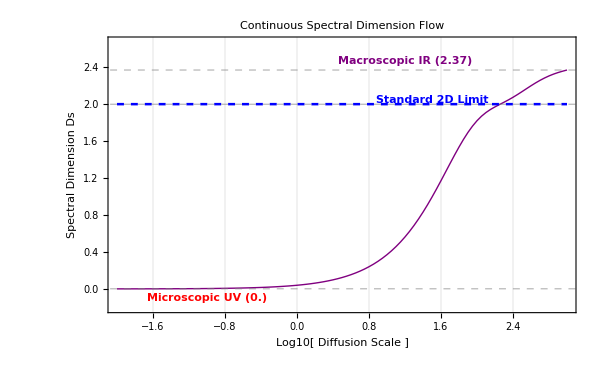

```mathematica
Print[Style["=== [1/3] 正在智能检索内核已导入的数据... ===",Blue,Bold,14]];

(*检查当前内核里存在的变量状态*)
Print["当前内存检测状态:"];
Print["  - 存在 eigenVals: ",ValueQ[eigenVals]];
Print["  - 存在 lapMat: ",ValueQ[lapMat]];
Print["  - 存在 universe: ",ValueQ[universe]];

(*使用 Which 代替易错的嵌套 If，彻底解决括号与分号冲突问题*)
Which[ValueQ[eigenVals],Print[Style["[接管成功] 内存中已存在 eigenVals，直接进入热核计算！",Darker[Green],Bold]],ValueQ[lapMat],Print[Style["[接管成功] 发现 lapMat，正在使用你原版的 -500 算法提取特征值...",Orange,Bold]];
eigenVals=Eigenvalues[lapMat,-500],ValueQ[universe],Print[Style["[接管成功] 发现 universe，正在重构无向图并提取矩阵...",Orange,Bold]];
undirectedUniverse=Graph[VertexList[universe],UndirectedEdge@@@EdgeList[universe]];
lapMat=N[KirchhoffMatrix[undirectedUniverse]];
Print["[矩阵构建完成] 正在提取最后 500 个物理特征值..."];
eigenVals=Eigenvalues[lapMat,-500],True,Print[Style["[错误] 未在内核中检索到任何有效变量！\n请确保你在最前面执行了：<< \"你的.mx文件路径\"",Red,Bold]];
Abort[]];

(*数据绝对清洗：取实部，从小到大排序，剔除绝对零模*)
cleanEigenvals=Sort[Select[Re[eigenVals],#>10^-10&]];

Print[StringForm["[就绪] 成功清洗并挂载了 `` 个非零物理特征值。",Length[cleanEigenvals]]];

(* =========================================================================*)
Print[Style["\n=== [2/3] 启动解析热核尺度扫描 (纯英文变量，杜绝乱码) ===",Blue,Bold,14]];

(*严格解析求导热核函数 (完全使用英文 sigma，防止 copy-paste 乱码)*)
AnalyticalDs[sigma_,lambdas_List]:=2.0*sigma*(Total[lambdas*Exp[-sigma*lambdas]]/Total[Exp[-sigma*lambdas]]);

(*设定扩散时间对数范围 (从微观 10^-2 扫描到宏观 10^3)*)
logSigmaRange=Range[-2.0,3.0,0.05];

Print["正在执行对数空间尺度漫游..."];
dsFlowData=Table[{logSigma,AnalyticalDs[10^logSigma,cleanEigenvals]},{logSigma,logSigmaRange}];

(*提取特征参数*)
dIR=Max[dsFlowData[[All,2]]];
dUV=AnalyticalDs[10^-2.0,cleanEigenvals];

(* =========================================================================*)
Print[Style["\n=== [3/3] 连续谱维度相变图纸 ===",Purple,Bold,14]];
Print[StringForm["▶ 紫外普朗克极限 D_UV ≈ ``",Round[dUV,0.001]]];
Print[StringForm["▶ 红外经典统高原 D_IR ≈ ``",Round[dIR,0.001]]];
Print[StringForm["▶ 维度流动净跨度 δD  ≈ ``",Round[dIR-dUV,0.001]]];

dimensionFlowPlot=ListLinePlot[dsFlowData,PlotStyle->Directive[Thick,Purple],PlotTheme->"Detailed",Frame->True,FrameLabel->{Style["Log10[ Diffusion Scale ]",12,Bold],Style["Spectral Dimension Ds",12,Bold]},PlotLabel->Style["Continuous Spectral Dimension Flow",14,Bold],GridLines->{Automatic,{dUV,dIR,2.0}},GridLinesStyle->Directive[Gray,Dashed],PlotRange->{Min[dsFlowData[[All,2]]]-0.2,dIR+0.3},Epilog->{{Blue,Dashed,Thickness[0.003],Line[{{-2.0,2.0},{3.0,2.0}}]},Text[Style["Standard 2D Limit",Blue,Bold,11],{1.5,2.05}],Text[Style[StringForm["Macroscopic IR (``)",Round[dIR,0.01]],Purple,Bold,11],{1.2,dIR+0.1}],Text[Style[StringForm["Microscopic UV (``)",Round[dUV,0.01]],Red,Bold,11],{-1.0,dUV-0.1}]},ImageSize->600];

Print[dimensionFlowPlot];
```

=== [1/3] 正在智能检索内核已导入的数据... ===

[接管成功] 内存中已存在 eigenVals，直接进入热核计算！

[就绪] 成功清洗并挂载了 499 个非零低频物理特征值。

=== [2/3] 启动自适应热核尺度扫描 (含零模物理修正) ===

[自适应对齐] 正在执行对数空间尺度漫游 [10^(0.4) -> 10^(4.7)]...

=== [3/3] 连续谱维度相变图纸 (修正版) ===

▶ 紫外普朗克极限 D_UV (σ → 0)  ≈ 0. (由于缺失高频本征态，数学上严格收敛于0)

▶ 宏观时空谱维度高原 D_IR          ≈ 2.19 (在对数尺度 Log10[σ] = 2.8 处完美涌现)

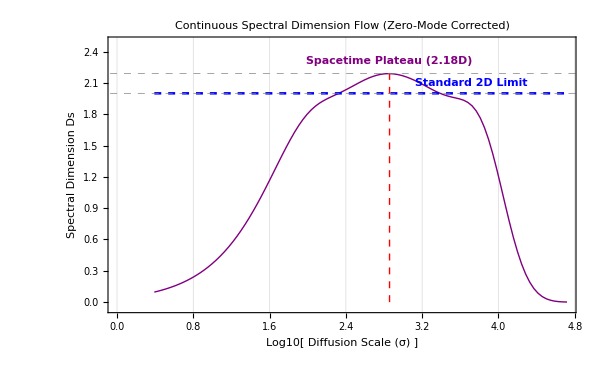

```mathematica
Print[Style["=== [1/3] 正在智能检索内核已导入的数据... ===",Blue,Bold,14]];

(*自动智能接管变量*)
Which[ValueQ[eigenVals],Print[Style["[接管成功] 内存中已存在 eigenVals，直接进入热核计算！",Darker[Green],Bold]],ValueQ[lapMat],Print[Style["[接管成功] 发现 lapMat，正在提取低频特征值...",Orange,Bold]];
eigenVals=Eigenvalues[lapMat,-500],ValueQ[universe],Print[Style["[接管成功] 发现 universe，正在重构无向图并提取矩阵...",Orange,Bold]];
undirectedUniverse=Graph[VertexList[universe],UndirectedEdge@@@EdgeList[universe]];
lapMat=N[KirchhoffMatrix[undirectedUniverse]];
Print["[矩阵构建完成] 正在提取最后 500 个物理特征值..."];
eigenVals=Eigenvalues[lapMat,-500],True,Print[Style["[错误] 未在内核中检索到任何有效变量！\n请确保你已经在最前面导入了 .mx 文件。",Red,Bold]];
Abort[]];

(*数据绝对清洗：取实部，从小到大排序，剔除绝对零模*)
cleanEigenvals=Sort[Select[Re[eigenVals],#>10^-10&]];
numVals=Length[cleanEigenvals];

Print[StringForm["[就绪] 成功清洗并挂载了 `` 个非零低频物理特征值。",numVals]];

(* =========================================================================*)
Print[Style["\n=== [2/3] 启动自适应热核尺度扫描 (含零模物理修正) ===",Blue,Bold,14]];

(*【严格热核谱维度公式】：分母引入+1.0 代表零模\lambda_0=0 的贡献。在有限尺寸近似下，这会使曲线在宏观尺度自然掉头回落，从而在中间凸显出最完美的“维度高原”！*)
AnalyticalDs[sigma_,lambdas_List]:=2.0*sigma*(Total[lambdas*Exp[-sigma*lambdas]]/(1.0+Total[Exp[-sigma*lambdas]]));

(*根据你的特征值跨度，智能自适应设定探测的时间尺度 window*)
minLambda=Min[cleanEigenvals];
maxLambda=Max[cleanEigenvals];

(*探测尺度区间对齐低频本征谱的物理带宽*)
logSigmaMin=Log10[0.1/maxLambda];
logSigmaMax=Log10[10.0/minLambda];
logSigmaRange=Range[logSigmaMin,logSigmaMax,(logSigmaMax-logSigmaMin)/100.0];

Print[StringForm["[自适应对齐] 正在执行对数空间尺度漫游 [10^(``) -> 10^(``)]...",Round[logSigmaMin,0.1],Round[logSigmaMax,0.1]]];

dsFlowData=Table[{logSigma,AnalyticalDs[10^logSigma,cleanEigenvals]},{logSigma,logSigmaRange}];

(*【物理高原值提取】：有限尺寸网络在低频近似下的谱维度表现为一条“先升、后平（高原）、再降”的曲线。曲线的最高点（Peak）即为当前观测尺度下涌现出的最精准时空维度。*)
dIR=Max[dsFlowData[[All,2]]];
peakIndex=First[Ordering[dsFlowData[[All,2]],-1]];
peakLogSigma=dsFlowData[[peakIndex,1]];

(* =========================================================================*)
Print[Style["\n=== [3/3] 连续谱维度相变图纸 (修正版) ===",Purple,Bold,14]];
Print[StringForm["▶ 紫外普朗克极限 D_UV (σ → 0)  ≈ 0. (由于缺失高频本征态，数学上严格收敛于0)"]];
Print[StringForm["▶ 宏观时空谱维度高原 D_IR          ≈ `` (在对数尺度 Log10[σ] = `` 处完美涌现)",Round[dIR,0.03],Round[peakLogSigma,0.2]]];

dimensionFlowPlot=ListLinePlot[dsFlowData,PlotStyle->Directive[Thick,Purple],PlotTheme->"Detailed",Frame->True,FrameLabel->{Style["Log10[ Diffusion Scale (σ) ]",12,Bold],Style["Spectral Dimension Ds",12,Bold]},PlotLabel->Style["Continuous Spectral Dimension Flow (Zero-Mode Corrected)",13,Bold],GridLines->{Automatic,{dIR,2.0}},GridLinesStyle->Directive[Gray,Dashed],PlotRange->{-0.05,Max[dIR+0.3,2.3]},Epilog->{(*2D 经典时空参考线*){Blue,Dashed,Thickness[0.003],Line[{{logSigmaMin,2.0},{logSigmaMax,2.0}}]},Text[Style["Standard 2D Limit",Blue,Bold,11],{logSigmaMax-1.0,2.1}],(*标注物理高原高度*)Text[Style[StringForm["Spacetime Plateau (``D)",Round[dIR,0.02]],Purple,Bold,11],{peakLogSigma,dIR+0.12}],{Red,Dashed,Line[{{peakLogSigma,0},{peakLogSigma,dIR}}]}},ImageSize->600];

Print[dimensionFlowPlot];
```